Research on Functions to get Neural Net Weights

```mathematica
NetInitialize
NetExtract
NetReplace, NetReplacePart
NetGraph
```

Initializing the Neural Net with Random Weights (Thresholding)

```mathematica
thresholdNetwork=NetChain[{LinearLayer[50, "Input"-> 50],ElementwiseLayer[If[#>0,1,0]&] }];
initializedThresholdNetwork=NetInitialize[thresholdNetwork, Method->{"Random","Biases"->NormalDistribution[],"Weights"->NormalDistribution[]},RandomSeeding->Automatic];
weights=NetExtract[initializedThresholdNetwork,{1,"Weights"}];
```

Pass Sample Outputs Through the Neural Net to see the Output

{29/50,0.00652535}

{1,0.0025766}

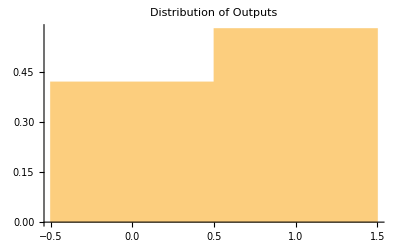

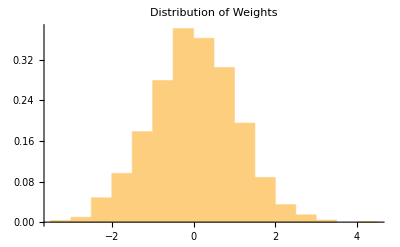

```mathematica
numSamples=1000;
sampleInputs=ConstantArray[ConstantArray[0, 50],numSamples];
outputs=initializedThresholdNetwork/@sampleInputs;
meanOutputs=Mean[Flatten[outputs]];
meanWeights=Mean[Flatten[Normal[weights]]];
{meanOutputs,meanWeights}
medianOutputs=Median[Flatten[outputs]];
medianWeights=Median[Flatten[Normal[weights]]];
{medianOutputs,medianWeights}
Histogram[Flatten[outputs],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Outputs"]
Histogram[Flatten[weights],Automatic,"ProbabilityDensity",PlotLabel->"Distribution of Weights"]
```

```mathematica
{19/50,Mean[NumericArray[…]]}
```

{19/50,Mean[NumericArray[…]]}

If the distribution of weights is negatively skewed, then the majority of outputs will be 0, and if the opposite is true, the majority of outputs will be 1.

Table::nliter: Non-list iterator depth at position 2 does not evaluate to a real numeric value.

Catenate::argx: Catenate called with 2 arguments; 1 argument is expected.

NetChain::netcontarg1: First argument of NetChain should be a list or an association of valid nets.

$Failed

NetInitialize::arg1: First argument to NetInitialize should be a net or list of nets.

NetInitialize[$Failed,Method→{Random,Biases→NormalDistribution[0,1]},RandomSeeding→Automatic]